# Two-dimensional diffusion FEM

## 缪雨轩 / Miao Yuxuan · 淮南师范学院 / Huainan Normal University

## Model, inputs and scope

∇⊥.b2Ez−jωμσEz=0; Jz=σEz

SI; exp(+j omega t); RMS; sigma=58 MS/m; mu_r=1; 20 C

Change mesh_h; run at least three meshes before making a convergence claim.

## Derivation and interpretation

The circular cross section solves ∇⊥.b2Ez−jωμσEz=0. A constant boundary field is normalized to the total complex current; the circle polygon, interpolation order and mesh size determine numerical error.

The weak form integrates ∇v·∇Ez+jωμσvEz over the domain, subject to the stated boundary value. Integrate the resulting current and Joule density independently and compare Rac with the Bessel solution.

This tutorial uses one mesh. Repeat at three or more decreasing h/a values and inspect boundary/polygon resolution before claiming accuracy; integral conservation alone does not bound field error.

```mathematica
projectRoot=NestWhile[DirectoryName,NotebookDirectory[],!FileExistsQ[FileNameJoin[{#1,"pyproject.toml"}]]&&DirectoryName[#1]=!=#1&];Get[FileNameJoin[{projectRoot,"shared","wolfram","ResearchNotebook.wl"}]];
```

## Editable parameters

```mathematica
parameters=<|"mesh_h"->0.2|>;parameters
```

<|mesh_h -> 0.2|>

## Independent execution and results

```mathematica
research=LitzNotebook`RunResearch[projectRoot,"fem2",parameters];LitzNotebook`ResearchSummary[research]
```

<|run_id -> notebook_fem2_20261014074655_f147273a, 
 
>   source_model -> 2D_circular_conductor_diffusion_FEM, 
 
>   execution_status -> completed, 
 
>   physical_acceptance_status -> passed_test_scope_only|>

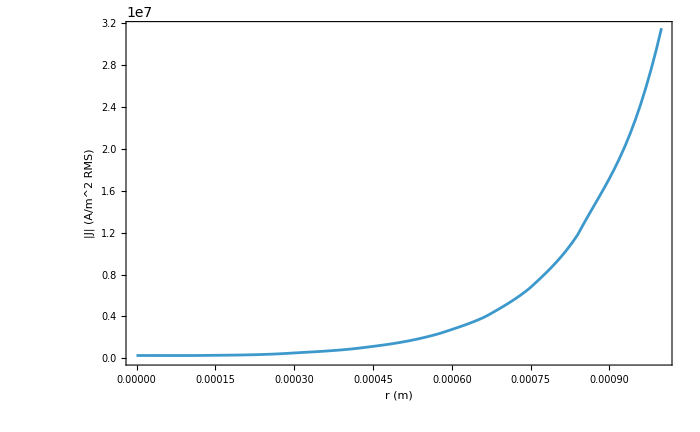

```mathematica
LitzNotebook`DisplayResearch[research]
```

## Acceptance and continuation

Inspect checks, execution_status and physical_acceptance_status. Continue full convergence and structural studies through the route README.

Sources: FEMDOC, P04; references/library.bib and references/sources.json

## Historical evidence

data/evidence/v1.0.0-rc.1/; litz-research data fetch fem2